## 3 nodes give this result

```mathematica
allGraphs//Length
```

15

```mathematica
IntegerDigits[13,3]
```

{1,1,1}

```mathematica
allGraphs[13,"graph"]
```

-Graphics-

```mathematica
(x-3)allGraphs[13,"colofourrealnull"]
```

(2 n123-n12x3-n13x2-n1x23+n1x2x3) (-3+x)

```mathematica
(x-2)allGraphs[13,"colofourrealnull"]/.x->3
```

2 n123-n12x3-n13x2-n1x23+n1x2x3

```mathematica
FromDigits[{1,1,1,1,1,1},3]
```

364

```mathematica
lambdaKey
```

20665

```mathematica
FromDigits[{1,1,1,1,1,1,1,1,1,1},3]
```

29524

```mathematica
k5Key
```

29524

```mathematica
ChromaticPolynomial[allGraphs[13,"graph"],x]//Factor
```

(-2+x) (-1+x) x

```mathematica
ChromaticPolynomial[EdgeAdd[allGraphs[13,"graph"],{1<->4,2<->4,3<->4}],x]//Factor
```

(-3+x) (-2+x) (-1+x) x

```mathematica
ChromaticPolynomial[CompleteGraph[4],x]//Factor
```

(-3+x) (-2+x) (-1+x) x

```mathematica
EdgeAdd[allGraphs[13,"graph"],{1<->4,2<->4,3<->4}]//ChromaticPolynomial//Factor
```

Function[x,-6 x+11 x^2-6 x^3+x^4]

```mathematica
vars=ListofVars[Simplify[allGraphs[13,"colofourrealnull"](x-2)-(allGraphs[13,"colofourrealnull"])]/.x->4]
```

{n1x2x3x4,n1x234,n1x23x4,n1x24x3,n1x2x34}

```mathematica
f=allGraphs[13,"colofourrealnull"](x-2)-(allGraphs[13,"colofourrealnull"])
```

-2 n1x234+n1x23x4+n1x24x3+n1x2x34-n1x2x3x4+(2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4) (-2+x)

```mathematica
Table[{Coefficient[f,v],v},{v,vars}]//TraditionalForm
```

(x-3 | n1x2x3x4
2 x-6 | n1x234
3-x | n1x23x4
3-x | n1x24x3
3-x | n1x2x34)

```mathematica
Fold[Plus,Map[#[[1]]*#[[2]]&,Table[{Coefficient[f,v],v},{v,vars}]]]//TraditionalForm
```

n1x234 (2 x-6)+n1x23x4 (3-x)+n1x24x3 (3-x)+n1x2x34 (3-x)+n1x2x3x4 (x-3)

## 4 nodes give this result

```mathematica
FromDigits[{1,0,1,1,0,1},3]
```

280

```mathematica
allGraphs[FromDigits[{1,0,1,1,0,1},3],"graph"]
```

-Graphics-

```mathematica
allGraphs[280,"colofourrealnull"]
```

-3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4

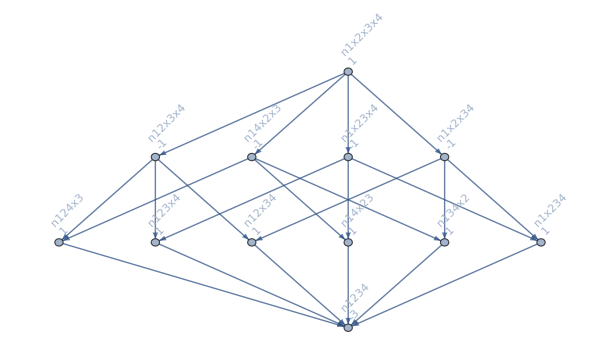

```mathematica
MobiusGraph[280]
```

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k, Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},VertexCount[g]==4&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->1]]&]}]
```

{-Graphics-364,-Graphics-361,-Graphics-283,-Graphics-280}

```mathematica
allGraphs[13,"colofourrealnull"]
```

```mathematica
vars=ListofVars[Simplify[allGraphs[280,"colofourrealnull"](x-3)-(allGraphs[280,"colofourrealnull"]+allGraphs[283,"colofourrealnull"])]/.x->4]
```

{n12x3x4,n14x2x3,n1x23x4,n1x24x3,n1x2x34,n1234,n123x4,n124x3,n12x34,n134x2,n14x23,n1x234,n1x2x3x4}

```mathematica
f=allGraphs[280,"colofourrealnull"](x-3)-(allGraphs[280,"colofourrealnull"]+allGraphs[283,"colofourrealnull"])
```

7 n1234-2 n123x4-3 n124x3-2 n12x34+2 n12x3x4-2 n134x2-2 n14x23+2 n14x2x3-3 n1x234+2 n1x23x4+n1x24x3+2 n1x2x34-2 n1x2x3x4+(-3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4) (-3+x)

```mathematica
Table[{Coefficient[f,v],v},{v,vars}]//TraditionalForm
```

(5-x | n12x3x4
5-x | n14x2x3
5-x | n1x23x4
1 | n1x24x3
5-x | n1x2x34
16-3 x | n1234
x-5 | n123x4
x-6 | n124x3
x-5 | n12x34
x-5 | n134x2
x-5 | n14x23
x-6 | n1x234
x-5 | n1x2x3x4)

```mathematica
Fold[Plus,Map[#[[1]]*#[[2]]&,Table[{Coefficient[f,v],v},{v,vars}]]]//TraditionalForm
```

n1234 (16-3 x)+n123x4 (x-5)+n124x3 (x-6)+n12x34 (x-5)+n12x3x4 (5-x)+n134x2 (x-5)+n14x23 (x-5)+n14x2x3 (5-x)+n1x234 (x-6)+n1x23x4 (5-x)+n1x24x3+n1x2x34 (5-x)+n1x2x3x4 (x-5)

```mathematica
n1x24x3+n1234 (16-3 x)+n12x3x4 (5-x)+n14x2x3 (5-x)+n1x23x4 (5-x)+n1x2x34 (5-x)+n124x3 (-6+x)+n1x234 (-6+x)+n123x4 (-5+x)+n12x34 (-5+x)+n134x2 (-5+x)+n14x23 (-5+x)+n1x2x3x4 (-5+x)==7 n1234-2 n123x4-3 n124x3-2 n12x34+2 n12x3x4-2 n134x2-2 n14x23+2 n14x2x3-3 n1x234+2 n1x23x4+n1x24x3+2 n1x2x34-2 n1x2x3x4+(-3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4) (-3+x)//Simplify
```

True

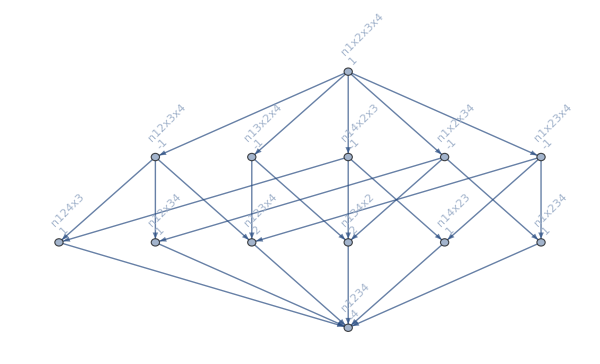

```mathematica
MobiusGraph[361]
```

```mathematica
MobiusGraph[280]
```

## 5 nodes give this result

```mathematica
IntegerDigits[lambdaKey,3]
```

{1,0,0,1,1,0,0,1,0,1}

```mathematica
FromDigits[{1,0,0,1,1,0,0,1,0,1},3]
```

20665

```mathematica
allGraphs[FromDigits[{1,0,0,1,1,0,0,1,0,1},3],"graph"]
```

-Graphics-

```mathematica
allGraphs[lambdaKey,"colofourrealnull"]
```

4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k, Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},VertexCount[g]==5&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]&&EdgeCount[g]==6]&]}]
```

{-Graphics-27226,-Graphics-22852,-Graphics-20746,-Graphics-20692,-Graphics-20668}

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k, Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},VertexCount[g]==5&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]&&EdgeCount[g]==7]&]}]
```

{-Graphics-29413,-Graphics-27307,-Graphics-27253,-Graphics-27229,-Graphics-22933,-Graphics-22879,-Graphics-22855,-Graphics-20773,-Graphics-20749,-Graphics-20695}

```mathematica
f/.repToComplete/.demoValues/.x->4
```

239

```mathematica
Table[allGraphs[k,"graph"],{k,{29413,20773,20668}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
f=allGraphs[lambdaKey,"colofourrealnull"](x-2)-(allGraphs[29413,"colofourrealnull"]+allGraphs[20773,"colofourrealnull"]+allGraphs[20668,"colofourrealnull"])//Simplify
```

-22 n12345+7 n1234x5+7 n1235x4+4 n123x45-4 n123x4x5+7 n1245x3-2 n124x3x5+4 n125x34-4 n125x3x4+4 n12x345-3 n12x34x5-n12x35x4-3 n12x3x45+3 n12x3x4x5+7 n1345x2-2 n134x2x5-2 n135x2x4-n13x2x45+n13x2x4x5+4 n145x23-4 n145x2x3-n14x23x5+n14x2x3x5+4 n15x234-3 n15x23x4-n15x24x3-3 n15x2x34+3 n15x2x3x4+7 n1x2345-4 n1x234x5-2 n1x235x4-3 n1x23x45+3 n1x23x4x5-2 n1x245x3+n1x24x3x5-n1x25x34+n1x25x3x4-4 n1x2x345+3 n1x2x34x5+n1x2x35x4+3 n1x2x3x45-3 n1x2x3x4x5+(4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5) (-2+x)

```mathematica
vars=ListofVars[f/.x->4]//DeleteDuplicates
```

{n13x2x4x5,n14x2x3x5,n1x24x3x5,n1x25x3x4,n1x2x35x4,n12345,n1234x5,n1235x4,n123x45,n123x4x5,n1245x3,n124x3x5,n125x34,n125x3x4,n12x345,n12x34x5,n12x35x4,n12x3x45,n12x3x4x5,n1345x2,n134x2x5,n135x2x4,n13x2x45,n145x23,n145x2x3,n14x23x5,n15x234,n15x23x4,n15x24x3,n15x2x34,n15x2x3x4,n1x2345,n1x234x5,n1x235x4,n1x23x45,n1x23x4x5,n1x245x3,n1x25x34,n1x2x345,n1x2x34x5,n1x2x3x45,n1x2x3x4x5}

```mathematica
Length[vars]
```

42

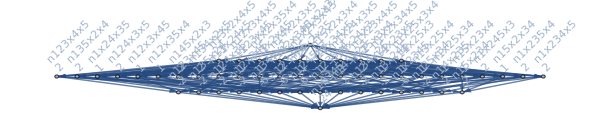

```mathematica
mg=MobiusGraph[k5Key]
```

```mathematica
InverseRealNull=Association[];Table[InverseRealNull[allGraphs[v,"colofourrealnull"]]=v,{v,realyNullAtomKeys}]
```

{0,2,6,18,26,54,72,162,168,218,486,488,546,666,728,1458,1476,1620,1944,2124,4374,4380,4428,4860,4920,5834,6320,13122,13124,13176,13284,13340,14586,14748,17514,17568,18980,39366,39368,39372,39384,39392,40878,40896,43902,43908,45416,52974,52976,54492,57528,59048}

```mathematica
repRotate=Table[allGraphs[v,"colofour"]->Rotate[allGraphs[v,"colofour"],Pi/4],{v,atomKeys}]
```

{v1x2x3x4x5→v1x2x3x4x5,v1x2x3x45→v1x2x3x45,v1x2x35x4→v1x2x35x4,v1x2x34x5→v1x2x34x5,v1x2x345→v1x2x345,v1x25x3x4→v1x25x3x4,v1x25x34→v1x25x34,v1x24x3x5→v1x24x3x5,v1x24x35→v1x24x35,v1x245x3→v1x245x3,v1x23x4x5→v1x23x4x5,v1x23x45→v1x23x45,v1x235x4→v1x235x4,v1x234x5→v1x234x5,v1x2345→v1x2345,v15x2x3x4→v15x2x3x4,v15x2x34→v15x2x34,v15x24x3→v15x24x3,v15x23x4→v15x23x4,v15x234→v15x234,v14x2x3x5→v14x2x3x5,v14x2x35→v14x2x35,v14x25x3→v14x25x3,v14x23x5→v14x23x5,v14x235→v14x235,v145x2x3→v145x2x3,v145x23→v145x23,v13x2x4x5→v13x2x4x5,v13x2x45→v13x2x45,v13x25x4→v13x25x4,v13x24x5→v13x24x5,v13x245→v13x245,v135x2x4→v135x2x4,v135x24→v135x24,v134x2x5→v134x2x5,v134x25→v134x25,v1345x2→v1345x2,v12x3x4x5→v12x3x4x5,v12x3x45→v12x3x45,v12x35x4→v12x35x4,v12x34x5→v12x34x5,v12x345→v12x345,v125x3x4→v125x3x4,v125x34→v125x34,v124x3x5→v124x3x5,v124x35→v124x35,v1245x3→v1245x3,v123x4x5→v123x4x5,v123x45→v123x45,v1235x4→v1235x4,v1234x5→v1234x5,v12345→v12345}

```mathematica
repToComplete=Table[allGraphs[v,"colofourrealnull"]->allGraphs[v,"colofour"],{v,realyNullAtomKeys}]
```

{n1x2x3x4x5→v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,n1x2x3x45→v12345+v123x45+v1245x3+v12x345+v12x3x45+v1345x2+v13x245+v13x2x45+v145x23+v145x2x3+v1x2345+v1x23x45+v1x245x3+v1x2x345+v1x2x3x45,n1x2x35x4→v12345+v1235x4+v124x35+v12x345+v12x35x4+v1345x2+v135x24+v135x2x4+v14x235+v14x2x35+v1x2345+v1x235x4+v1x24x35+v1x2x345+v1x2x35x4,n1x2x34x5→v12345+v1234x5+v125x34+v12x345+v12x34x5+v1345x2+v134x25+v134x2x5+v15x234+v15x2x34+v1x2345+v1x234x5+v1x25x34+v1x2x345+v1x2x34x5,n1x2x345→v12345+v12x345+v1345x2+v1x2345+v1x2x345,n1x25x3x4→v12345+v1235x4+v1245x3+v125x34+v125x3x4+v134x25+v13x245+v13x25x4+v14x235+v14x25x3+v1x2345+v1x235x4+v1x245x3+v1x25x34+v1x25x3x4,n1x25x34→v12345+v125x34+v134x25+v1x2345+v1x25x34,n1x24x3x5→v12345+v1234x5+v1245x3+v124x35+v124x3x5+v135x24+v13x245+v13x24x5+v15x234+v15x24x3+v1x2345+v1x234x5+v1x245x3+v1x24x35+v1x24x3x5,n1x24x35→v12345+v124x35+v135x24+v1x2345+v1x24x35,n1x245x3→v12345+v1245x3+v13x245+v1x2345+v1x245x3,n1x23x4x5→v12345+v1234x5+v1235x4+v123x45+v123x4x5+v145x23+v14x235+v14x23x5+v15x234+v15x23x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5,n1x23x45→v12345+v123x45+v145x23+v1x2345+v1x23x45,n1x235x4→v12345+v1235x4+v14x235+v1x2345+v1x235x4,n1x234x5→v12345+v1234x5+v15x234+v1x2345+v1x234x5,n1x2345→v12345+v1x2345,n15x2x3x4→v12345+v1235x4+v1245x3+v125x34+v125x3x4+v1345x2+v135x24+v135x2x4+v145x23+v145x2x3+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4,n15x2x34→v12345+v125x34+v1345x2+v15x234+v15x2x34,n15x24x3→v12345+v1245x3+v135x24+v15x234+v15x24x3,n15x23x4→v12345+v1235x4+v145x23+v15x234+v15x23x4,n15x234→v12345+v15x234,n14x2x3x5→v12345+v1234x5+v1245x3+v124x35+v124x3x5+v1345x2+v134x25+v134x2x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5,n14x2x35→v12345+v124x35+v1345x2+v14x235+v14x2x35,n14x25x3→v12345+v1245x3+v134x25+v14x235+v14x25x3,n14x23x5→v12345+v1234x5+v145x23+v14x235+v14x23x5,n14x235→v12345+v14x235,n145x2x3→v12345+v1245x3+v1345x2+v145x23+v145x2x3,n145x23→v12345+v145x23,n13x2x4x5→v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5,n13x2x45→v12345+v123x45+v1345x2+v13x245+v13x2x45,n13x25x4→v12345+v1235x4+v134x25+v13x245+v13x25x4,n13x24x5→v12345+v1234x5+v135x24+v13x245+v13x24x5,n13x245→v12345+v13x245,n135x2x4→v12345+v1235x4+v1345x2+v135x24+v135x2x4,n135x24→v12345+v135x24,n134x2x5→v12345+v1234x5+v1345x2+v134x25+v134x2x5,n134x25→v12345+v134x25,n1345x2→v12345+v1345x2,n12x3x4x5→v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5,n12x3x45→v12345+v123x45+v1245x3+v12x345+v12x3x45,n12x35x4→v12345+v1235x4+v124x35+v12x345+v12x35x4,n12x34x5→v12345+v1234x5+v125x34+v12x345+v12x34x5,n12x345→v12345+v12x345,n125x3x4→v12345+v1235x4+v1245x3+v125x34+v125x3x4,n125x34→v12345+v125x34,n124x3x5→v12345+v1234x5+v1245x3+v124x35+v124x3x5,n124x35→v12345+v124x35,n1245x3→v12345+v1245x3,n123x4x5→v12345+v1234x5+v1235x4+v123x45+v123x4x5,n123x45→v12345+v123x45,n1235x4→v12345+v1235x4,n1234x5→v12345+v1234x5,n12345→v12345}

```mathematica
Table[{GraphDistance[mg,v,n12345],Coefficient[f,v],v/.repcolofourrealnullgraph2,allGraphs[InverseRealNull[v],"colofour"]/.demoValues,allGraphs[InverseRealNull[v],"colofour"]/.repRotate},{v,vars}]//Sort//TableForm
```

0 | -30+4 x | -Graphics-n1234559048 | 68 | v12345
1 | 6-x | -Graphics-n123x4552976 | 170 | v12345+v123x45
1 | 6-x | -Graphics-n125x3440896 | 163 | v12345+v125x34
1 | 6-x | -Graphics-n12x34539392 | 146 | v12345+v12x345
1 | 6-x | -Graphics-n145x236320 | 211 | v12345+v145x23
1 | 6-x | -Graphics-n15x2342124 | 170 | v12345+v15x234
1 | 9-x | -Graphics-n1234x557528 | 172 | v12345+v1234x5
1 | 9-x | -Graphics-n1235x454492 | 136 | v12345+v1235x4
1 | 9-x | -Graphics-n1245x345416 | 136 | v12345+v1245x3
1 | 9-x | -Graphics-n1345x218980 | 136 | v12345+v1345x2
1 | 9-x | -Graphics-n1x2345728 | 131 | v12345+v1x2345
2 | -2 | -Graphics-n124x3x543902 | 344 | v12345+v1234x5+v1245x3+v124x35+v124x3x5
2 | -2 | -Graphics-n134x2x517514 | 344 | v12345+v1234x5+v1345x2+v134x25+v134x2x5
2 | -2 | -Graphics-n135x2x414586 | 272 | v12345+v1235x4+v1345x2+v135x24+v135x2x4
2 | -2 | -Graphics-n1x235x4546 | 262 | v12345+v1235x4+v14x235+v1x2345+v1x235x4
2 | -2 | -Graphics-n1x245x3218 | 262 | v12345+v1245x3+v13x245+v1x2345+v1x245x3
2 | -1 | -Graphics-n12x35x439372 | 292 | v12345+v1235x4+v124x35+v12x345+v12x35x4
2 | -1 | -Graphics-n14x23x54860 | 446 | v12345+v1234x5+v145x23+v14x235+v14x23x5
2 | -1 | -Graphics-n13x2x4513124 | 340 | v12345+v123x45+v1345x2+v13x245+v13x2x45
2 | -1 | -Graphics-n15x24x31620 | 340 | v12345+v1245x3+v135x24+v15x234+v15x24x3
2 | -1 | -Graphics-n1x25x3472 | 328 | v12345+v125x34+v134x25+v1x2345+v1x25x34
2 | -6+x | -Graphics-n123x4x552974 | 544 | v12345+v1234x5+v1235x4+v123x45+v123x4x5
2 | -6+x | -Graphics-n125x3x440878 | 420 | v12345+v1235x4+v1245x3+v125x34+v125x3x4
2 | -6+x | -Graphics-n1x234x5666 | 438 | v12345+v1234x5+v15x234+v1x2345+v1x234x5
2 | -6+x | -Graphics-n145x2x35834 | 524 | v12345+v1245x3+v1345x2+v145x23+v145x2x3
2 | -6+x | -Graphics-n1x2x34526 | 364 | v12345+v12x345+v1345x2+v1x2345+v1x2x345
2 | -5+x | -Graphics-n12x34x539384 | 478 | v12345+v1234x5+v125x34+v12x345+v12x34x5
2 | -5+x | -Graphics-n12x3x4539368 | 406 | v12345+v123x45+v1245x3+v12x345+v12x3x45
2 | -5+x | -Graphics-n15x23x41944 | 496 | v12345+v1235x4+v145x23+v15x234+v15x23x4
2 | -5+x | -Graphics-n1x23x45488 | 450 | v12345+v123x45+v145x23+v1x2345+v1x23x45
2 | -5+x | -Graphics-n15x2x341476 | 452 | v12345+v125x34+v1345x2+v15x234+v15x2x34
3 | 1 | -Graphics-n13x2x4x513122 | 1088 | v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5
3 | 1 | -Graphics-n14x2x3x54374 | 1112 | v12345+v1234x5+v1245x3+v124x35+v124x3x5+v1345x2+v134x25+v134x2x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5
3 | 1 | -Graphics-n1x24x3x5162 | 876 | v12345+v1234x5+v1245x3+v124x35+v124x3x5+v135x24+v13x245+v13x24x5+v15x234+v15x24x3+v1x2345+v1x234x5+v1x245x3+v1x24x35+v1x24x3x5
3 | 1 | -Graphics-n1x25x3x454 | 876 | v12345+v1235x4+v1245x3+v125x34+v125x3x4+v134x25+v13x245+v13x25x4+v14x235+v14x25x3+v1x2345+v1x235x4+v1x245x3+v1x25x34+v1x25x3x4
3 | 1 | -Graphics-n1x2x35x46 | 728 | v12345+v1235x4+v124x35+v12x345+v12x35x4+v1345x2+v135x24+v135x2x4+v14x235+v14x2x35+v1x2345+v1x235x4+v1x24x35+v1x2x345+v1x2x35x4
3 | 5-x | -Graphics-n12x3x4x539366 | 1368 | v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5
3 | 5-x | -Graphics-n1x23x4x5486 | 1380 | v12345+v1234x5+v1235x4+v123x45+v123x4x5+v145x23+v14x235+v14x23x5+v15x234+v15x23x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5
3 | 5-x | -Graphics-n1x2x34x518 | 1240 | v12345+v1234x5+v125x34+v12x345+v12x34x5+v1345x2+v134x25+v134x2x5+v15x234+v15x2x34+v1x2345+v1x234x5+v1x25x34+v1x2x345+v1x2x34x5
3 | 5-x | -Graphics-n15x2x3x41458 | 1344 | v12345+v1235x4+v1245x3+v125x34+v125x3x4+v1345x2+v135x24+v135x2x4+v145x23+v145x2x3+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4
3 | 5-x | -Graphics-n1x2x3x452 | 1208 | v12345+v123x45+v1245x3+v12x345+v12x3x45+v1345x2+v13x245+v13x2x45+v145x23+v145x2x3+v1x2345+v1x23x45+v1x245x3+v1x2x345+v1x2x3x45
4 | -5+x | -Graphics-n1x2x3x4x50 | 3728 | v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5

```mathematica
Fold[Plus,Map[#[[1]]*#[[2]]&,Table[{Coefficient[f,v],v},{v,vars}]]]
```

-2 n124x3x5-n12x35x4-2 n134x2x5-2 n135x2x4-n13x2x45+n13x2x4x5-n14x23x5+n14x2x3x5-n15x24x3-2 n1x235x4-2 n1x245x3+n1x24x3x5-n1x25x34+n1x25x3x4+n1x2x35x4+n12x3x4x5 (5-x)+n15x2x3x4 (5-x)+n1x23x4x5 (5-x)+n1x2x34x5 (5-x)+n1x2x3x45 (5-x)+n123x45 (6-x)+n125x34 (6-x)+n12x345 (6-x)+n145x23 (6-x)+n15x234 (6-x)+n1234x5 (9-x)+n1235x4 (9-x)+n1245x3 (9-x)+n1345x2 (9-x)+n1x2345 (9-x)+n123x4x5 (-6+x)+n125x3x4 (-6+x)+n145x2x3 (-6+x)+n1x234x5 (-6+x)+n1x2x345 (-6+x)+n12x34x5 (-5+x)+n12x3x45 (-5+x)+n15x23x4 (-5+x)+n15x2x34 (-5+x)+n1x23x45 (-5+x)+n1x2x3x4x5 (-5+x)+n12345 (-30+4 x)

```mathematica
Simplify[Fold[Plus,Map[#[[1]]*#[[2]]&,Table[{Coefficient[f,v],v},{v,vars}]]]==f]
```

True

## Table of formulas

```mathematica
{{3 nodes, -Graphics-, n1x234 (2 x-6)+n1x23x4 (3-x)+n1x24x3 (3-x)+n1x2x34 (3-x)+n1x2x3x4 (x-3)}, {4 nodes, -Graphics-, n1234 (16-3 x)+n123x4 (x-5)+n124x3 (x-6)+n12x34 (x-5)+n12x3x4 (5-x)+n134x2 (x-5)+n14x23 (x-5)+
n14x2x3 (5-x)+n1x234 (x-6)+n1x23x4 (5-x)+n1x24x3+n1x2x34 (5-x)+n1x2x3x4 (x-5)}, {5 nodes, -Graphics-, n12345 (4 x-34)+n1234x5 (10-x)+n1235x4 (10-x)+n123x45 (7-x)+n123x4x5 (x-7)+n1245x3 (10-x)
-2 n124x3x5+n125x34 (7-x)+n125x3x4 (x-7)+n12x345 (7-x)+n12x34x5 (x-6)-n12x35x4+n12x3x45 (x-6)
+n12x3x4x5 (6-x)+n1345x2 (10-x)-2 n134x2x5-2 n135x2x4-n13x2x45+n13x2x4x5+n145x23 (7-x)
+n145x2x3 (x-7)-n14x23x5+n14x2x3x5+n15x234 (7-x)+n15x23x4 (x-6)
-n15x24x3+n15x2x34 (x-6)+n15x2x3x4 (6-x)+n1x2345 (10-x)+n1x234x5 (x-7)
-2 n1x235x4+n1x23x45 (x-6)+n1x23x4x5 (6-x)-2 n1x245x3+n1x24x3x5
-n1x25x34+n1x25x3x4+n1x2x345 (x-7)+n1x2x34x5 (6-x)+n1x2x35x4+n1x2x3x45 (6-x)+n1x2x3x4x5 (x-6)}}
```

```mathematica
n1x234 (2 x-6)+n1x23x4 (3-x)+n1x24x3 (3-x)+n1x2x34 (3-x)+n1x2x3x4 (x-3)/.x->4
```

2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4

```mathematica
n1234 (16-3 x)+n123x4 (x-5)+n124x3 (x-6)+n12x34 (x-5)+n12x3x4 (5-x)+n134x2 (x-5)+n14x23 (x-5)+
n14x2x3 (5-x)+n1x234 (x-6)+n1x23x4 (5-x)+n1x24x3+n1x2x34 (5-x)+n1x2x3x4 (x-5)/.x->4
```

4 n1234-n123x4-2 n124x3-n12x34+n12x3x4-n134x2-n14x23+n14x2x3-2 n1x234+n1x23x4+n1x24x3+n1x2x34-n1x2x3x4

```mathematica
(n12345 (4 x-34)+n1234x5 (10-x)+n1235x4 (10-x)+n123x45 (7-x)+n123x4x5 (x-7)+n1245x3 (10-x)-2 n124x3x5+n125x34 (7-x)+n125x3x4 (x-7)+n12x345 (7-x)+n12x34x5 (x-6)-n12x35x4+n12x3x45 (x-6)+n12x3x4x5 (6-x)+n1345x2 (10-x)-2 n134x2x5-2 n135x2x4-n13x2x45+n13x2x4x5+n145x23 (7-x)+n145x2x3 (x-7)-n14x23x5+n14x2x3x5+n15x234 (7-x)+n15x23x4 (x-6)-n15x24x3+n15x2x34 (x-6)+n15x2x3x4 (6-x)+n1x2345 (10-x)+n1x234x5 (x-7)-2 n1x235x4+n1x23x45 (x-6)+n1x23x4x5 (6-x)-2 n1x245x3+n1x24x3x5-n1x25x34+n1x25x3x4+n1x2x345 (x-7)+n1x2x34x5 (6-x)+n1x2x35x4+n1x2x3x45 (6-x)+n1x2x3x4x5 (x-6)/.repToComplete//Expand)/.repcolofourgraph2
```

```mathematica
First[Select[allGraphs,#["colofourrealnull"]==n1x2x3x4x5&]]["graph"]
```

-Graphics-

```mathematica
Expand[-2 n124x3x5-n12x35x4-2 n134x2x5-2 n135x2x4-n13x2x45+n13x2x4x5-n14x23x5+n14x2x3x5-n15x24x3-2 n1x235x4-2 n1x245x3+n1x24x3x5-n1x25x34+n1x25x3x4+n1x2x35x4+n12x3x4x5 (5-x)+n15x2x3x4 (5-x)+n1x23x4x5 (5-x)+n1x2x34x5 (5-x)+n1x2x3x45 (5-x)+n123x45 (6-x)+n125x34 (6-x)+n12x345 (6-x)+n145x23 (6-x)+n15x234 (6-x)+n1234x5 (9-x)+n1235x4 (9-x)+n1245x3 (9-x)+n1345x2 (9-x)+n1x2345 (9-x)+n123x4x5 (-6+x)+n125x3x4 (-6+x)+n145x2x3 (-6+x)+n1x234x5 (-6+x)+n1x2x345 (-6+x)+n12x34x5 (-5+x)+n12x3x45 (-5+x)+n15x23x4 (-5+x)+n15x2x34 (-5+x)+n1x23x45 (-5+x)+n1x2x3x4x5 (-5+x)+n12345 (-30+4 x)/.repToComplete]/.repcolofourgraph2/.x->0
```

-3 -Graphics-v13x24x536166-3 -Graphics-v13x25x436112-3 -Graphics-v14x25x331738-3 -Graphics-v14x2x3531714-3 -Graphics-v1x24x3529608-4 -Graphics-v13x2x4x536085-4 -Graphics-v14x2x3x531711-4 -Graphics-v1x24x3x529605-4 -Graphics-v1x25x3x429551-4 -Graphics-v1x2x35x429527-5 -Graphics-v1x2x3x4x529524

```mathematica
Table[
Expand[-2 n124x3x5-n12x35x4-2 n134x2x5-2 n135x2x4-n13x2x45+n13x2x4x5-n14x23x5+n14x2x3x5-n15x24x3-2 n1x235x4-2 n1x245x3+n1x24x3x5-n1x25x34+n1x25x3x4+n1x2x35x4+n12x3x4x5 (5-x)+n15x2x3x4 (5-x)+n1x23x4x5 (5-x)+n1x2x34x5 (5-x)+n1x2x3x45 (5-x)+n123x45 (6-x)+n125x34 (6-x)+n12x345 (6-x)+n145x23 (6-x)+n15x234 (6-x)+n1234x5 (9-x)+n1235x4 (9-x)+n1245x3 (9-x)+n1345x2 (9-x)+n1x2345 (9-x)+n123x4x5 (-6+x)+n125x3x4 (-6+x)+n145x2x3 (-6+x)+n1x234x5 (-6+x)+n1x2x345 (-6+x)+n12x34x5 (-5+x)+n12x3x45 (-5+x)+n15x23x4 (-5+x)+n15x2x34 (-5+x)+n1x23x45 (-5+x)+n1x2x3x4x5 (-5+x)+n12345 (-30+4 x)/.repToComplete]/.x->k,
{k,-1,3}]
```

{-4 v13x24x5-4 v13x25x4-5 v13x2x4x5-4 v14x25x3-4 v14x2x35-5 v14x2x3x5-4 v1x24x35-5 v1x24x3x5-5 v1x25x3x4-5 v1x2x35x4-6 v1x2x3x4x5,-3 v13x24x5-3 v13x25x4-4 v13x2x4x5-3 v14x25x3-3 v14x2x35-4 v14x2x3x5-3 v1x24x35-4 v1x24x3x5-4 v1x25x3x4-4 v1x2x35x4-5 v1x2x3x4x5,-2 v13x24x5-2 v13x25x4-3 v13x2x4x5-2 v14x25x3-2 v14x2x35-3 v14x2x3x5-2 v1x24x35-3 v1x24x3x5-3 v1x25x3x4-3 v1x2x35x4-4 v1x2x3x4x5,-v13x24x5-v13x25x4-2 v13x2x4x5-v14x25x3-v14x2x35-2 v14x2x3x5-v1x24x35-2 v1x24x3x5-2 v1x25x3x4-2 v1x2x35x4-3 v1x2x3x4x5,-v13x2x4x5-v14x2x3x5-v1x24x3x5-v1x25x3x4-v1x2x35x4-2 v1x2x3x4x5}

```mathematica
vars2=ListofVars[-4 v13x24x5-4 v13x25x4-5 v13x2x4x5-4 v14x25x3-4 v14x2x35-5 v14x2x3x5-4 v1x24x35-5 v1x24x3x5-5 v1x25x3x4-5 v1x2x35x4-6 v1x2x3x4x5]//Sort
```

{v13x24x5,v13x25x4,v13x2x4x5,v14x25x3,v14x2x35,v14x2x3x5,v1x24x35,v1x24x3x5,v1x25x3x4,v1x2x35x4,v1x2x3x4x5}

```mathematica
TableForm[
Table[
With[
{fred=Expand[-2 n124x3x5-n12x35x4-2 n134x2x5-2 n135x2x4-n13x2x45+n13x2x4x5-n14x23x5+n14x2x3x5-n15x24x3-2 n1x235x4-2 n1x245x3+n1x24x3x5-n1x25x34+n1x25x3x4+n1x2x35x4+n12x3x4x5 (5-x)+n15x2x3x4 (5-x)+n1x23x4x5 (5-x)+n1x2x34x5 (5-x)+n1x2x3x45 (5-x)+n123x45 (6-x)+n125x34 (6-x)+n12x345 (6-x)+n145x23 (6-x)+n15x234 (6-x)+n1234x5 (9-x)+n1235x4 (9-x)+n1245x3 (9-x)+n1345x2 (9-x)+n1x2345 (9-x)+n123x4x5 (-6+x)+n125x3x4 (-6+x)+n145x2x3 (-6+x)+n1x234x5 (-6+x)+n1x2x345 (-6+x)+n12x34x5 (-5+x)+n12x3x45 (-5+x)+n15x23x4 (-5+x)+n15x2x34 (-5+x)+n1x23x45 (-5+x)+n1x2x3x4x5 (-5+x)+n12345 (-30+4 x)/.repToComplete]/.x->k},
Prepend[Table[Coefficient[fred,v],{v,vars2}],k]
],
{k,-1,10}
],
TableHeadings->{None,Prepend[vars2/.repcolofourgraph2,"k"]}
]
```

k | -Graphics-v13x24x536166 | -Graphics-v13x25x436112 | -Graphics-v13x2x4x536085 | -Graphics-v14x25x331738 | -Graphics-v14x2x3531714 | -Graphics-v14x2x3x531711 | -Graphics-v1x24x3529608 | -Graphics-v1x24x3x529605 | -Graphics-v1x25x3x429551 | -Graphics-v1x2x35x429527 | -Graphics-v1x2x3x4x529524
-1 | -4 | -4 | -5 | -4 | -4 | -5 | -4 | -5 | -5 | -5 | -6
0 | -3 | -3 | -4 | -3 | -3 | -4 | -3 | -4 | -4 | -4 | -5
1 | -2 | -2 | -3 | -2 | -2 | -3 | -2 | -3 | -3 | -3 | -4
2 | -1 | -1 | -2 | -1 | -1 | -2 | -1 | -2 | -2 | -2 | -3
3 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | -1 | -1 | -2
4 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | -1
5 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 0
6 | 3 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 1
7 | 4 | 4 | 3 | 4 | 4 | 3 | 4 | 3 | 3 | 3 | 2
8 | 5 | 5 | 4 | 5 | 5 | 4 | 5 | 4 | 4 | 4 | 3
9 | 6 | 6 | 5 | 6 | 6 | 5 | 6 | 5 | 5 | 5 | 4
10 | 7 | 7 | 6 | 7 | 7 | 6 | 7 | 6 | 6 | 6 | 5

```mathematica
HornerForm[-2 n124x3x5-n12x35x4-2 n134x2x5-2 n135x2x4-n13x2x45+n13x2x4x5-n14x23x5+n14x2x3x5-n15x24x3-2 n1x235x4-2 n1x245x3+n1x24x3x5-n1x25x34+n1x25x3x4+n1x2x35x4+n12x3x4x5 (5-x)+n15x2x3x4 (5-x)+n1x23x4x5 (5-x)+n1x2x34x5 (5-x)+n1x2x3x45 (5-x)+n123x45 (6-x)+n125x34 (6-x)+n12x345 (6-x)+n145x23 (6-x)+n15x234 (6-x)+n1234x5 (9-x)+n1235x4 (9-x)+n1245x3 (9-x)+n1345x2 (9-x)+n1x2345 (9-x)+n123x4x5 (-6+x)+n125x3x4 (-6+x)+n145x2x3 (-6+x)+n1x234x5 (-6+x)+n1x2x345 (-6+x)+n12x34x5 (-5+x)+n12x3x45 (-5+x)+n15x23x4 (-5+x)+n15x2x34 (-5+x)+n1x23x45 (-5+x)+n1x2x3x4x5 (-5+x)+n12345 (-30+4 x),x]
```

-30 n12345+9 n1234x5+9 n1235x4+6 n123x45-6 n123x4x5+9 n1245x3-2 n124x3x5+6 n125x34-6 n125x3x4+6 n12x345-5 n12x34x5-n12x35x4-5 n12x3x45+5 n12x3x4x5+9 n1345x2-2 n134x2x5-2 n135x2x4-n13x2x45+n13x2x4x5+6 n145x23-6 n145x2x3-n14x23x5+n14x2x3x5+6 n15x234-5 n15x23x4-n15x24x3-5 n15x2x34+5 n15x2x3x4+9 n1x2345-6 n1x234x5-2 n1x235x4-5 n1x23x45+5 n1x23x4x5-2 n1x245x3+n1x24x3x5-n1x25x34+n1x25x3x4-6 n1x2x345+5 n1x2x34x5+n1x2x35x4+5 n1x2x3x45-5 n1x2x3x4x5+(4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5) x

```mathematica
Solve[-30 n12345+9 n1234x5+9 n1235x4+6 n123x45-6 n123x4x5+9 n1245x3-2 n124x3x5+6 n125x34-6 n125x3x4+6 n12x345-5 n12x34x5-n12x35x4-5 n12x3x45+5 n12x3x4x5+9 n1345x2-2 n134x2x5-2 n135x2x4-n13x2x45+n13x2x4x5+6 n145x23-6 n145x2x3-n14x23x5+n14x2x3x5+6 n15x234-5 n15x23x4-n15x24x3-5 n15x2x34+5 n15x2x3x4+9 n1x2345-6 n1x234x5-2 n1x235x4-5 n1x23x45+5 n1x23x4x5-2 n1x245x3+n1x24x3x5-n1x25x34+n1x25x3x4-6 n1x2x345+5 n1x2x34x5+n1x2x35x4+5 n1x2x3x45-5 n1x2x3x4x5+(4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5) x==0,x]
```

{{x→(30 n12345-9 n1234x5-9 n1235x4-6 n123x45+6 n123x4x5-9 n1245x3+2 n124x3x5-6 n125x34+6 n125x3x4-6 n12x345+5 n12x34x5+n12x35x4+5 n12x3x45-5 n12x3x4x5-9 n1345x2+2 n134x2x5+2 n135x2x4+n13x2x45-n13x2x4x5-6 n145x23+6 n145x2x3+n14x23x5-n14x2x3x5-6 n15x234+5 n15x23x4+n15x24x3+5 n15x2x34-5 n15x2x3x4-9 n1x2345+6 n1x234x5+2 n1x235x4+5 n1x23x45-5 n1x23x4x5+2 n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4+6 n1x2x345-5 n1x2x34x5-n1x2x35x4-5 n1x2x3x45+5 n1x2x3x4x5)/(4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5)}}

```mathematica
ListofVars[Numerator[(30 n12345-9 n1234x5-9 n1235x4-6 n123x45+6 n123x4x5-9 n1245x3+2 n124x3x5-6 n125x34+6 n125x3x4-6 n12x345+5 n12x34x5+n12x35x4+5 n12x3x45-5 n12x3x4x5-9 n1345x2+2 n134x2x5+2 n135x2x4+n13x2x45-n13x2x4x5-6 n145x23+6 n145x2x3+n14x23x5-n14x2x3x5-6 n15x234+5 n15x23x4+n15x24x3+5 n15x2x34-5 n15x2x3x4-9 n1x2345+6 n1x234x5+2 n1x235x4+5 n1x23x45-5 n1x23x4x5+2 n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4+6 n1x2x345-5 n1x2x34x5-n1x2x35x4-5 n1x2x3x45+5 n1x2x3x4x5)/(4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5)]]//Length
```

42

```mathematica
ListofVars[Denominator[(30 n12345-9 n1234x5-9 n1235x4-6 n123x45+6 n123x4x5-9 n1245x3+2 n124x3x5-6 n125x34+6 n125x3x4-6 n12x345+5 n12x34x5+n12x35x4+5 n12x3x45-5 n12x3x4x5-9 n1345x2+2 n134x2x5+2 n135x2x4+n13x2x45-n13x2x4x5-6 n145x23+6 n145x2x3+n14x23x5-n14x2x3x5-6 n15x234+5 n15x23x4+n15x24x3+5 n15x2x34-5 n15x2x3x4-9 n1x2345+6 n1x234x5+2 n1x235x4+5 n1x23x45-5 n1x23x4x5+2 n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4+6 n1x2x345-5 n1x2x34x5-n1x2x35x4-5 n1x2x3x45+5 n1x2x3x4x5)/(4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5)]]//Length
```

27

```mathematica
Apart[(30 n12345-9 n1234x5-9 n1235x4-6 n123x45+6 n123x4x5-9 n1245x3+2 n124x3x5-6 n125x34+6 n125x3x4-6 n12x345+5 n12x34x5+n12x35x4+5 n12x3x45-5 n12x3x4x5-9 n1345x2+2 n134x2x5+2 n135x2x4+n13x2x45-n13x2x4x5-6 n145x23+6 n145x2x3+n14x23x5-n14x2x3x5-6 n15x234+5 n15x23x4+n15x24x3+5 n15x2x34-5 n15x2x3x4-9 n1x2345+6 n1x234x5+2 n1x235x4+5 n1x23x45-5 n1x23x4x5+2 n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4+6 n1x2x345-5 n1x2x34x5-n1x2x35x4-5 n1x2x3x45+5 n1x2x3x4x5)/(4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5)]
```

```mathematica
5+(10 n12345-4 n1234x5-4 n1235x4-n123x45+n123x4x5-4 n1245x3+2 n124x3x5-n125x34+n125x3x4-n12x345+n12x35x4-4 n1345x2+2 n134x2x5+2 n135x2x4+n13x2x45-n13x2x4x5-n145x23+n145x2x3+n14x23x5-n14x2x3x5-n15x234+n15x24x3-4 n1x2345+n1x234x5+2 n1x235x4+2 n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4+n1x2x345-n1x2x35x4)/(4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5)/.repToComplete/.demoValues
```

1605/461

```mathematica
Reduce[(10 n12345-4 n1234x5-4 n1235x4-n123x45+n123x4x5-4 n1245x3+2 n124x3x5-n125x34+n125x3x4-n12x345+n12x35x4-4 n1345x2+2 n134x2x5+2 n135x2x4+n13x2x45-n13x2x4x5-n145x23+n145x2x3+n14x23x5-n14x2x3x5-n15x234+n15x24x3-4 n1x2345+n1x234x5+2 n1x235x4+2 n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4+n1x2x345-n1x2x35x4)/(4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5)==-1]
```

n12345==1/14 (5 n1234x5+5 n1235x4+2 n123x45-2 n123x4x5+5 n1245x3-2 n124x3x5+2 n125x34-2 n125x3x4+2 n12x345-n12x34x5-n12x35x4-n12x3x45+n12x3x4x5+5 n1345x2-2 n134x2x5-2 n135x2x4-n13x2x45+n13x2x4x5+2 n145x23-2 n145x2x3-n14x23x5+n14x2x3x5+2 n15x234-n15x23x4-n15x24x3-n15x2x34+n15x2x3x4+5 n1x2345-2 n1x234x5-2 n1x235x4-n1x23x45+n1x23x4x5-2 n1x245x3+n1x24x3x5-n1x25x34+n1x25x3x4-2 n1x2x345+n1x2x34x5+n1x2x35x4+n1x2x3x45-n1x2x3x4x5)&&3 n1234x5+3 n1235x4-3 n123x45+3 n123x4x5+3 n1245x3-4 n124x3x5-3 n125x34+3 n125x3x4-3 n12x345+5 n12x34x5-2 n12x35x4+5 n12x3x45-5 n12x3x4x5+3 n1345x2-4 n134x2x5-4 n135x2x4-2 n13x2x45+2 n13x2x4x5-3 n145x23+3 n145x2x3-2 n14x23x5+2 n14x2x3x5-3 n15x234+5 n15x23x4-2 n15x24x3+5 n15x2x34-5 n15x2x3x4+3 n1x2345+3 n1x234x5-4 n1x235x4+5 n1x23x45-5 n1x23x4x5-4 n1x245x3+2 n1x24x3x5-2 n1x25x34+2 n1x25x3x4+3 n1x2x345-5 n1x2x34x5+2 n1x2x35x4-5 n1x2x3x45+5 n1x2x3x4x5≠0

```mathematica
n12345-1/14 (5 n1234x5+5 n1235x4+2 n123x45-2 n123x4x5+5 n1245x3-2 n124x3x5+2 n125x34-2 n125x3x4+2 n12x345-n12x34x5-n12x35x4-n12x3x45+n12x3x4x5+5 n1345x2-2 n134x2x5-2 n135x2x4-n13x2x45+n13x2x4x5+2 n145x23-2 n145x2x3-n14x23x5+n14x2x3x5+2 n15x234-n15x23x4-n15x24x3-n15x2x34+n15x2x3x4+5 n1x2345-2 n1x234x5-2 n1x235x4-n1x23x45+n1x23x4x5-2 n1x245x3+n1x24x3x5-n1x25x34+n1x25x3x4-2 n1x2x345+n1x2x34x5+n1x2x35x4+n1x2x3x45-n1x2x3x4x5)/.repToComplete/.demoValues
```

-239/14

## Varibles that are not used in wheelgraphs

```mathematica
v17=ListofVars[(30 n12345-9 n1234x5-9 n1235x4-6 n123x45+6 n123x4x5-9 n1245x3+2 n124x3x5-6 n125x34+6 n125x3x4-6 n12x345+5 n12x34x5+n12x35x4+5 n12x3x45-5 n12x3x4x5-9 n1345x2+2 n134x2x5+2 n135x2x4+n13x2x45-n13x2x4x5-6 n145x23+6 n145x2x3+n14x23x5-n14x2x3x5-6 n15x234+5 n15x23x4+n15x24x3+5 n15x2x34-5 n15x2x3x4-9 n1x2345+6 n1x234x5+2 n1x235x4+5 n1x23x45-5 n1x23x4x5+2 n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4+6 n1x2x345-5 n1x2x34x5-n1x2x35x4-5 n1x2x3x45+5 n1x2x3x4x5)/(4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5)]//DeleteDuplicates
```

```mathematica
Complement[realyNullAtomVars,v17]/.repcolofourrealnullgraph2//Sort
```

{-Graphics-n124x3543908,-Graphics-n14x2354920,-Graphics-n135x2414748,-Graphics-n13x24513340,-Graphics-n134x2517568,-Graphics-n13x24x513284,-Graphics-n13x25x413176,-Graphics-n14x25x34428,-Graphics-n14x2x354380,-Graphics-n1x24x35168}

```mathematica
Complement[realyNullAtomVars,v17]/.repToComplete/.repcolofourgraph2//Sort//TableForm
```

-Graphics-v1234559048+-Graphics-v124x3551478
-Graphics-v1234559048+-Graphics-v14x23531984
-Graphics-v1234559048+-Graphics-v135x2436898
-Graphics-v1234559048+-Graphics-v13x24536194
-Graphics-v1234559048+-Graphics-v134x2538308
-Graphics-v1234559048+-Graphics-v1234x558288+-Graphics-v135x2436898+-Graphics-v13x24536194+-Graphics-v13x24x536166
-Graphics-v1234559048+-Graphics-v1235x456770+-Graphics-v13x24536194+-Graphics-v134x2538308+-Graphics-v13x25x436112
-Graphics-v1234559048+-Graphics-v1245x352232+-Graphics-v14x23531984+-Graphics-v134x2538308+-Graphics-v14x25x331738
-Graphics-v1234559048+-Graphics-v124x3551478+-Graphics-v1345x239014+-Graphics-v14x23531984+-Graphics-v14x2x3531714
-Graphics-v1234559048+-Graphics-v124x3551478+-Graphics-v1x234529888+-Graphics-v135x2436898+-Graphics-v1x24x3529608